## Larvae burden in diaphragm

### Data

```mathematica
dir = NotebookDirectory[]
```

R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\

```mathematica
FileNames["Polish*",dir]
```

{R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\Polish samples with LPG-abstract.xlsx}

```mathematica
infile = "R:\\Z&O\\Projecten\\Dier en Vector\\Parasitologie\\Trichinella QMRA\\Polish samples with LPG-abstract.xlsx"
```

R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\Polish samples with LPG-abstract.xlsx

```mathematica
df = Import[infile];
```

```mathematica
df= df[[1]];
```

```mathematica
lpg = df[[2;;,7]]
```

{7.6,4.02,0.3,42.8,33.1,12.,13.,0.3,41.,1.9,4.,10.,2.4,1.4,6.,63.,4.92,0.22,89.,19.52,47.,2.4,3.,4.1,69.,4.92,56.,211.,0.8,0.9,94.,0.56,2.12,1.5}

```mathematica
lpg = IntegerPart[50 lpg]
```

{380,200,15,2140,1655,600,650,15,2050,95,200,500,120,70,300,3150,246,11,4450,976,2350,120,150,204,3450,246,2800,10550,40,45,4700,28,106,75}

```mathematica
{examined,positive}={685595,2832}
```

{685595,2832}

### Estimation

```mathematica
f=Binomial[x+k-1,k-1] (m/k)^x(1+m/k)^(-k-x)
```

(m/k)^x (1+m/k)^(-k-x) Binomial[-1+k+x,-1+k]

```mathematica
g = N@LogLikelihood[BinomialDistribution[examined,1-f/.x-> 0],{positive}]
```

18367.+682763. Log[(1.+m/k)^(-1. k)]+2832. Log[1.-1. (1.+m/k)^(-1. k)]

```mathematica
lik=.
```

```mathematica
lik:=∏_(i=1)^n (f/.{x->Subscript[x, i]})
```

```mathematica
lik
```

∏_(i=1)^n (m/k)^x_i (1+m/k)^(-k-x_i) Binomial[-1+k+x_i,-1+k]

```mathematica
Remove@obslik
obslik:=g +Log[lik]/.{n:>Length[lpg],Subscript[x, i_]:>lpg[[i]]}
```

```mathematica
sol = NMaximize[{obslik,0<m,0<k<1},{m,k}]
```

{-467.293,{m→5.24431,k→0.000447051}}

```mathematica
1-N@(positive/examined)
```

0.995869

```mathematica
Table[100f/.sol[[2]],{x,0,3}]
```

{99.582,0.0445145,0.0222653,0.0148456}

## Larvae recovery

### Data

```mathematica
dir = NotebookDirectory[]
```

R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\

```mathematica
FileNames["Larva*.xlsx",dir]
```

{R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\Larval recovery NL trich labs.xlsx}

```mathematica
infile="R:\\Z&O\\Projecten\\Dier en Vector\\Parasitologie\\Trichinella QMRA\\Larval recovery NL trich labs.xlsx"
```

R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\Larval recovery NL trich labs.xlsx

```mathematica
data=Import[infile]//First;
```

Exclude zero spike.

```mathematica
data=Cases[data,{x_,y_}/;0<x<1000];
```

{{5.,5.},{5.,5.},{7.,7.},{9.,4.},{5.,5.},{5.,4.},{7.,7.},{9.,4.},{5.,5.},{5.,4.},{7.,7.},{9.,6.},{5.,4.},{5.,4.},{7.,7.},{9.,4.},{9.,8.},{5.,5.},{5.,5.},{7.,6.},{9.,7.},{5.,6.},{5.,4.},{7.,7.},{9.,8.},{5.,5.},{5.,4.},{7.,6.},{5.,4.},{5.,3.},{7.,5.},{9.,9.},{5.,4.},{5.,3.},{7.,6.},{9.,9.},{5.,4.},{5.,3.},{7.,4.},{9.,8.},{7.,5.},{9.,8.},{5.,4.},{5.,3.},{7.,5.},{9.,6.},{5.,4.},{5.,4.},{7.,4.},{9.,8.},{5.,3.},{5.,2.},{3.,3.},{3.,2.},{8.,7.},{8.,6.},{3.,3.},{3.,3.},{8.,7.},{8.,6.},{3.,3.},{3.,2.},{8.,7.},{8.,6.},{3.,3.},{3.,3.},{8.,7.},{8.,6.},{3.,4.},{3.,3.},{8.,7.},{8.,8.},{3.,3.},{3.,3.},{8.,7.},{8.,7.},{3.,3.},{3.,3.},{8.,7.},{8.,8.},{3.,3.},{3.,2.},{8.,6.},{8.,5.},{3.,2.},{3.,2.},{8.,6.},{8.,5.},{3.,3.},{3.,2.},{8.,7.},{8.,5.},{3.,3.},{3.,1.},{8.,3.},{8.,5.},{3.,3.},{3.,1.},{8.,3.},{8.,6.},{3.,3.},{3.,1.},{8.,3.},{8.,6.},{3.,3.},{3.,1.},{8.,3.},{8.,5.},{3.,3.},{3.,1.},{8.,3.},{8.,6.},{3.,3.},{3.,1.},{8.,3.},{8.,6.},{5.,5.},{5.,4.},{9.,6.},{9.,7.},{5.,4.},{5.,3.},{9.,8.},{9.,7.},{5.,5.},{5.,3.},{9.,6.},{9.,7.},{5.,5.},{5.,4.},{9.,6.},{9.,6.},{9.,7.},{5.,4.},{9.,9.},{5.,4.},{9.,6.},{5.,5.},{9.,8.},{5.,6.},{9.,7.},{5.,4.},{9.,9.},{5.,4.},{5.,5.},{9.,8.},{5.,3.},{9.,8.},{5.,6.},{9.,8.},{5.,3.},{9.,8.},{5.,5.},{9.,7.},{5.,3.},{9.,8.},{5.,5.},{9.,10.},{5.,3.},{9.,8.},{4.,4.},{8.,6.},{6.,6.},{8.,8.},{4.,5.},{8.,8.},{6.,6.},{8.,8.},{4.,2.},{8.,5.},{6.,6.},{8.,7.},{4.,3.},{8.,6.},{6.,6.},{8.,8.},{4.,4.},{8.,6.},{6.,6.},{8.,8.},{8.,7.},{4.,3.},{8.,8.},{6.,6.},{8.,5.},{4.,4.},{8.,8.},{6.,6.},{8.,5.},{4.,4.},{8.,7.},{6.,6.},{8.,6.},{4.,4.},{8.,7.},{6.,5.},{6.,6.},{8.,8.},{8.,8.},{4.,4.},{6.,5.},{8.,6.},{8.,7.},{4.,4.},{6.,4.},{8.,6.},{8.,6.},{4.,4.},{8.,6.},{4.,4.},{6.,5.},{8.,4.},{8.,5.},{4.,3.},{6.,3.},{8.,6.},{8.,6.},{4.,2.},{6.,3.},{8.,5.},{8.,7.},{4.,3.},{6.,4.},{8.,3.}}

```mathematica
{spike,recovered}=dataᵀ;
```

### Beta binomial model of a single larvae recovery

Parameters α and β are correlated. These transformations makes it easy to maximize the likelihood.

```mathematica
Solve[{α/(α+β)==u,Log[α+β]== v},{α,β}]
```

{{α→ConditionalExpression[ⅇ^v u,-π<Im[v]≤π],β→ConditionalExpression[ⅇ^v-ⅇ^v u,-π<Im[v]≤π]}}

Derive Beta Binomial distribution.

```mathematica
p=.
```

```mathematica
PDF[BinomialDistribution[n,p],x]
```

Piecewise[{{(1-p)^(n-x) p^x Binomial[n,x], 0≤x≤n}, {0, True}}]

```mathematica
PDF[BetaDistribution[a,b],p]
```

Piecewise[{{((1-p)^(-1+b) p^(-1+a))/Beta[a,b], 0<p<1}, {0, True}}]

Parameter mixture.

```mathematica
Integrate[(1-p)^(n-x) p^x Binomial[n,x] ((1-p)^(-1+b) p^(-1+a))/Beta[a,b],{p,0,1}]
```

ConditionalExpression[(Binomial[n,x] Gamma[b+n-x] Gamma[a+x])/(Beta[a,b] Gamma[a+b+n]),Re[a+x]>0&&Re[b+n-x]>0]

Apply the transformaion. Binomial term is constant for all parameter values. Drop it.

```mathematica
(Gamma[b+n-x] Gamma[a+x])/(Beta[a,b] Gamma[a+b+n])/.{a-> u ⅇ^v,b->(1-u)ⅇ^v}
```

(Gamma[n+ⅇ^v (1-u)-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,ⅇ^v (1-u)] Gamma[n+ⅇ^v (1-u)+ⅇ^v u])

Now sinplify.

```mathematica
FullSimplify@((Gamma[n+ⅇ^v (1-u)-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,ⅇ^v (1-u)] Gamma[n+ⅇ^v (1-u)+ⅇ^v u]))
```

(Gamma[ⅇ^v+n-ⅇ^v u-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,-ⅇ^v (-1+u)] Gamma[ⅇ^v+n])

Final difinition.

```mathematica
f=(Gamma[ⅇ^v+n-ⅇ^v u-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,-ⅇ^v (-1+u)] Gamma[ⅇ^v+n])
```

(Gamma[ⅇ^v+n-ⅇ^v u-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,-ⅇ^v (-1+u)] Gamma[ⅇ^v+n])

Define likelihood.

```mathematica
lik:=∏_(i=1)^s (f/.{n->Subscript[n, i],x->Subscript[x, i]})
```

Insert the data points.

```mathematica
obsloglik:=Log@lik/.{s:> Length[diaphragm],Subscript[n, i]:>spike[[i]],Subscript[x, i]:>recovered[[i]] }
```

Find the maximum likelihood estimates.

When I called the build in Beta binomial distribution, I found that the maximization fails due to memory bust.

Remember:
(1) Define function by your self.
(2) Define function using reals not integers.

```mathematica
nul = NMaximize[{obsloglik,0<u<1},{u,v}]
```

Estimated mean and variance.

```mathematica
{u,(u(1-u))/(1+ⅇ^v)}/.nul[[2]]
```

{0.841435,0.0472264}

Back transform the parameters.

```mathematica
{a-> u ⅇ^v,b->(1-u)ⅇ^v}/.nul[[2]]
```

{a→1.53575,b→0.289405}

```mathematica
beta = BetaDistribution[a,b]/.{a-> u ⅇ^v,b->(1-u)ⅇ^v}/.nul[[2]]
```

BetaDistribution[1.53575,0.289405]

Estimated beta distribution.

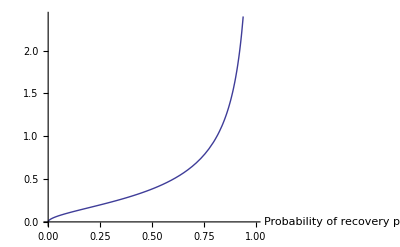

```mathematica
Plot[PDF[beta,x],{x,0,1},AxesLabel->{"Probability of recovery per larva",None}]
```

```mathematica
PDF[BetaBinomialDistribution[a,b,n],0]/.{a-> u ⅇ^v,b->(1-u)ⅇ^v}/.nul[[2]]
```

Piecewise[{{Pochhammer[0.289405,n]/Pochhammer[1.82516,n], 0≤n}, {0, True}}]

```mathematica
recoveryProbability = Table[1-Pochhammer[0.2894050520857973,n]/Pochhammer[1.8251553490608916,n],{n,1,10}];
```

```mathematica
TableForm[recoveryProbability,TableHeadings->Automatic]
```

1 | 0.841435
2 | 0.927631
3 | 0.956686
4 | 0.970472
5 | 0.978257
6 | 0.983149
7 | 0.986456
8 | 0.988813
9 | 0.990562
10 | 0.991901

```mathematica
PDF[BetaBinomialDistribution[a,b,n],x]
```

Piecewise[{{(Binomial[n,x] Pochhammer[a,x] Pochhammer[b,n-x])/Pochhammer[a+b,n], 0≤x≤n}, {0, True}}]

```mathematica
FunctionExpand@PDF[BetaBinomialDistribution[a,b,n],x]
```

Piecewise[{{(Gamma[a+b] Gamma[1+n] Gamma[b+n-x] Gamma[a+x])/(Gamma[a] Gamma[b] Gamma[a+b+n] Gamma[1+n-x] Gamma[1+x]), 0≤x≤n}, {0, True}}]

```mathematica
Simplify@FunctionExpand@PDF[BetaBinomialDistribution[a,b,n],0]
```

Piecewise[{{(Gamma[a+b] Gamma[b+n])/(Gamma[b] Gamma[a+b+n]), 0≤n}, {0, True}}]

```mathematica
FunctionExpand[Binomial[n,x] Beta[x+a,n-x+b]/Beta[a,b]]
```

(Gamma[a+b] Gamma[1+n] Gamma[b+n-x] Gamma[a+x])/(Gamma[a] Gamma[b] Gamma[a+b+n] Gamma[1+n-x] Gamma[1+x])

```mathematica
FullSimplify[Binomial[n,x] Beta[x+a,n-x+b]/Beta[a,b]-(Binomial[n,x] Pochhammer[a,x] Pochhammer[b,n-x])/Pochhammer[a+b,n]]
```

0

```mathematica
Binomial[n,x] Beta[x+a,n-x+b]/Beta[a,b]/.x->0
```

Beta[a,b+n]/Beta[a,b]

## Parasite numbers in 5 gram diaphragm

### Question A

From 50 gram if diapfragm only 5 gram (10%) is tested . What is the number of trichinella in 5 gram diaphragm? If the parasite number in 50 gram is negative binomial, is it also negative binomial in which the mean is scaled by 10%?

#### Answer: Negative binomial distribution where the mean is scaled by 10%.

This is a binomial distribution when the the parameter n is negative binomial distribution.

```mathematica
𝒟=ParameterMixtureDistribution[BinomialDistribution[n,p],n\[Distributed]NegativeBinomialDistribution[k,k/(k+m)]]
```

ParameterMixtureDistribution[BinomialDistribution[n,p],n\[Distributed]NegativeBinomialDistribution[k,k/(k+m)]]

This is the charateristic function.

```mathematica
cf1=CharacteristicFunction[𝒟,t]
```

k^k (k-(-1+ⅇ^(ⅈ t)) m p)^-k

Characteristic function of negative binomial distribution in which the mean is scaled by p.

```mathematica
cf2=Simplify@CharacteristicFunction[NegativeBinomialDistribution[k,k/(k+p m)],t]
```

(k/(k+m p-ⅇ^(ⅈ t) m p))^k

The two characteristics functions are equal. Hence, the mixture distribution is negative binomial distribution.

```mathematica
PowerExpand[cf2- ExpandAll@cf1 ]
```

0

### Question B:

The number of trichinella in 50 gram of diaphragm is negative binomial distribution. What is the number in 100 gram?

#### Answer: negative binomial distribution where both parameters are scaled by 2.

This is a binomial distribution when the the parameter n is negative binomial distribution.

```mathematica
𝒟=TransformedDistribution[x+y,{x\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],y\[Distributed]NegativeBinomialDistribution[k,k/(k+m)]} ]
```

NegativeBinomialDistribution[2 k,k/(k+m)]

This is the charateristic function.

```mathematica
cf1=Simplify@CharacteristicFunction[𝒟,t]
```

(k/(k+m-ⅇ^(ⅈ t) m))^(2 k)

Characteristic function of negative binomial distribution where both parameters are scaled by 2.

```mathematica
cf2=Simplify@CharacteristicFunction[NegativeBinomialDistribution[2 k,(2 k)/(2 k+2 m)],t]
```

(k/(k+m-ⅇ^(ⅈ t) m))^(2 k)

The two characteristics functions are equal. Hence, the mixture distribution is negative binomial distribution.

```mathematica
PowerExpand[cf2- ExpandAll@cf1 ]
```

0

### Question C:

The number of trichinella in 5 gram of diaphragm is negative binomial distribution. What is the number in 50 gram?

#### Answer: negative binomial distribution where both parameters are scaled by 10.

This is a binomial distribution when the the parameter n is negative binomial distribution.

```mathematica
vars = Array[Subscript[x, #]&,10]
```

{x_1,x_2,x_3,x_4,x_5,x_6,x_7,x_8,x_9,x_10}

```mathematica
dists=Thread[Distributed[vars,ConstantArray[ NegativeBinomialDistribution[k,k/(k+m)],10]]]
```

{x_1\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_2\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_3\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_4\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_5\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_6\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_7\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_8\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_9\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_10\[Distributed]NegativeBinomialDistribution[k,k/(k+m)]}

```mathematica
𝒟=TransformedDistribution[Total@vars,dists ]
```

NegativeBinomialDistribution[10 k,k/(k+m)]

This is the charateristic function.

```mathematica
cf1=Simplify@CharacteristicFunction[𝒟,t]
```

(k/(k+m-ⅇ^(ⅈ t) m))^(10 k)

Characteristic function of negative binomial distribution where both parameters are scaled by 2.

```mathematica
cf2=Simplify@CharacteristicFunction[NegativeBinomialDistribution[10 k,(10 k)/(10 k+10 m)],t]
```

(k/(k+m-ⅇ^(ⅈ t) m))^(10 k)

The two characteristics functions are equal. Hence, the mixture distribution is negative binomial distribution.

```mathematica
PowerExpand[cf2- ExpandAll@cf1 ]
```

0

## Safety test simulation

In Netherlands, 12 to 15  million domestic pigs slaghtered per year, 3000 wild boar slaughtered per year.

```mathematica
numberOfAnimals = 100000
```

100000

```mathematica
maxrange=2000000
```

2000000

```mathematica
proportionDiaphragm =N[ 5/100]
```

0.05

```mathematica
𝒩=NegativeBinomialDistribution[2 k,(2 k)/(2 k+2 m)]/.{m->5.244308845834319,k->0.00044705143472671417}
```

NegativeBinomialDistribution[0.000894103,0.0000852378]

```mathematica
p=Table[PDF[𝒩,x],{x,0,maxrange}];
```

```mathematica
𝒟=EmpiricalDistribution[p-> Range[0,maxrange]];
```

```mathematica
p=.
```

```mathematica
animal = RandomVariate[𝒟,numberOfAnimals]
```

```mathematica
infected = Position[animal,x_/;x>0];
```

```mathematica
diaphragm = MapAt[RandomVariate[BinomialDistribution[#,proportionDiaphragm]]&, animal,infected];
```

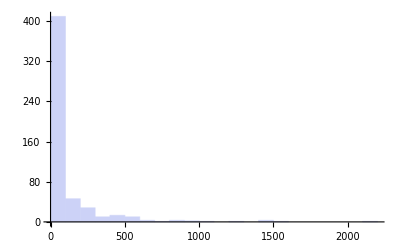

```mathematica
Histogram[ Extract[diaphragm, Position[diaphragm,x_/;x>0]]]
```

```mathematica
diaphragmBatch=Partition[diaphragm,20];
```

```mathematica
diaphragmBatch[[1;;3]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,70,0,0,0,0,0,0,0,0,0,0}}

```mathematica
animal[[1;;60]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1414,0,0,0,0,0,0,0,0,0,0}

```mathematica
batchID=Flatten@Array[ConstantArray[#,20]&,Length@diaphragmBatch];
```

```mathematica
Length[batchID]==Length[animal]
```

True

```mathematica
batchSum = Total/@diaphragmBatch;
```

```mathematica
batchSum[[4850;;4880]]
```

{0,0,0,0,0,16,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

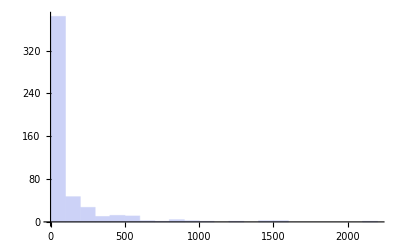

```mathematica
Histogram[ Extract[batchSum, Position[batchSum,x_/;x>0]]]
```

```mathematica
recoveryProbability = Map[1-Pochhammer[0.2894050520857973,#]/Pochhammer[1.8251553490608916,#]&,batchSum];
```

```mathematica
recoveryProbability[[4866]]
```

0.841435

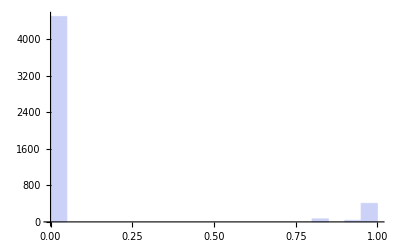

```mathematica
Histogram[recoveryProbability]
```

```mathematica
outcome = Map[RandomReal[]<#&,recoveryProbability];
```

```mathematica
outcome[[4866]]
```

False

```mathematica
Total[outcome]
```

4508 False+492 True

```mathematica
TableForm[SortBy[ {outcome,batchSum,recoveryProbability}ᵀ ,First ],TableHeadings->{Automatic,{"contaminated", "larvae","recovery prob"}}];
```

```mathematica
Tally@outcome
```

{{False,4508},{True,492}}

```mathematica
escapedBatchID = Cases[{Union@batchID,batchSum,outcome}ᵀ,{w_,x_,y_}/;x>0&&y==False:> w]
```

{235,653,827,1282,2012,2085,2674,3312,3361,3454,3628,3688,3835,4866,4933}

```mathematica
Length[{235,653,827,1282,2012,2085,2674,3312,3361,3454,3628,3688,3835,4866,4933}]
```

15

```mathematica
escapedAnimalID= Position[ batchID,x_/;MemberQ[escapedBatchID,x] ]
```

{{4681},{4682},{4683},{4684},{4685},{4686},{4687},{4688},{4689},{4690},{4691},{4692},{4693},{4694},{4695},{4696},{4697},{4698},{4699},{4700},{13041},{13042},{13043},{13044},{13045},{13046},{13047},{13048},{13049},{13050},{13051},{13052},{13053},{13054},{13055},{13056},{13057},{13058},{13059},{13060},{16521},{16522},{16523},{16524},{16525},{16526},{16527},{16528},{16529},{16530},{16531},{16532},{16533},{16534},{16535},{16536},{16537},{16538},{16539},{16540},{25621},{25622},{25623},{25624},{25625},{25626},{25627},{25628},{25629},{25630},{25631},{25632},{25633},{25634},{25635},{25636},{25637},{25638},{25639},{25640},{40221},{40222},{40223},{40224},{40225},{40226},{40227},{40228},{40229},{40230},{40231},{40232},{40233},{40234},{40235},{40236},{40237},{40238},{40239},{40240},{41681},{41682},{41683},{41684},{41685},{41686},{41687},{41688},{41689},{41690},{41691},{41692},{41693},{41694},{41695},{41696},{41697},{41698},{41699},{41700},{53461},{53462},{53463},{53464},{53465},{53466},{53467},{53468},{53469},{53470},{53471},{53472},{53473},{53474},{53475},{53476},{53477},{53478},{53479},{53480},{66221},{66222},{66223},{66224},{66225},{66226},{66227},{66228},{66229},{66230},{66231},{66232},{66233},{66234},{66235},{66236},{66237},{66238},{66239},{66240},{67201},{67202},{67203},{67204},{67205},{67206},{67207},{67208},{67209},{67210},{67211},{67212},{67213},{67214},{67215},{67216},{67217},{67218},{67219},{67220},{69061},{69062},{69063},{69064},{69065},{69066},{69067},{69068},{69069},{69070},{69071},{69072},{69073},{69074},{69075},{69076},{69077},{69078},{69079},{69080},{72541},{72542},{72543},{72544},{72545},{72546},{72547},{72548},{72549},{72550},{72551},{72552},{72553},{72554},{72555},{72556},{72557},{72558},{72559},{72560},{73741},{73742},{73743},{73744},{73745},{73746},{73747},{73748},{73749},{73750},{73751},{73752},{73753},{73754},{73755},{73756},{73757},{73758},{73759},{73760},{76681},{76682},{76683},{76684},{76685},{76686},{76687},{76688},{76689},{76690},{76691},{76692},{76693},{76694},{76695},{76696},{76697},{76698},{76699},{76700},{97301},{97302},{97303},{97304},{97305},{97306},{97307},{97308},{97309},{97310},{97311},{97312},{97313},{97314},{97315},{97316},{97317},{97318},{97319},{97320},{98641},{98642},{98643},{98644},{98645},{98646},{98647},{98648},{98649},{98650},{98651},{98652},{98653},{98654},{98655},{98656},{98657},{98658},{98659},{98660}}

```mathematica
batchID[[97303]]
```

4866

```mathematica
escapedAnimalID[[263]]
```

{97303}

```mathematica
animal[[97303]]
```

120

```mathematica
larvaeEscapedAnimal = Extract[animal,escapedAnimalID];
```

```mathematica
larvaeEscapedAnimal
```

{0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,57,0,0,0,0,0,0,0,0,0,0,0,0,0,17,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,92,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,51,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,73,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7,0,0,0,0,31,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,17,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0,0,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36,0,0,0}

```mathematica
Position[ larvaeEscapedAnimal, 120]
```

{{263}}

```mathematica
TableForm@Sort@Tally@larvaeEscapedAnimal
```

0 | 285
2 | 1
6 | 1
7 | 2
12 | 1
17 | 2
19 | 1
31 | 1
36 | 1
51 | 1
57 | 1
73 | 1
92 | 1
120 | 1